```mathematica
ClearAll["Global`*"]
```

```mathematica
M=1;α=3/10;
```

```mathematica
f[r_]:=1-(2M ⅇ^((-α M^(2/3))/r^2))/r
g[u_]:=1-2 M u ⅇ^(-u^2 α M^(2/3))
```

```mathematica
event=NSolveValues[f[r]==0,r]
```

NSolveValues::ifun: NSolveValues 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{0.447692,1.82833}

```mathematica
ev=event[[2]]
```

1.82833

```mathematica
sol=N@SolveValues[r^2-bc^2 f[r]==0&&2 bc^2 f[r]^2-r^3 D[f[r],r]==0&&2<r<3&&5<bc<6,{bc,r},Reals]
```

{{5.00833,2.81574}}

```mathematica
ss=sol[[1,1]]
```

5.00833

```mathematica
sss=sol[[1,2]]
```

2.81574

```mathematica
l[b0_]:=Module[{b=b0},FindInstance[1/b^2-x^2 g[x]==0&&0.36>x>0,{x},Reals]]
```

```mathematica
ϕ[b_]:=Chop[NIntegrate[1/Sqrt[1/b^2-x^2  g[x]],{x,0,l[b][[1,1,2]]}],10^-6]
(*OR ϕ[b_]:=Re[NIntegrate[1/Sqrt[1/b^2-x^2  g[x]],{x,0,l[b][[1,1,2]]}]]*)
```

```mathematica
ψ[b_]:=NIntegrate[1/Sqrt[1/b^2-x^2 g[x]],{x,0,1/ev}]
```

```mathematica
ϕ[19.75]
```

1.69048-3.05269×10^-7 ⅈ

```mathematica
ϕ[37.5]
```

1.62875-6.25053×10^-7 ⅈ

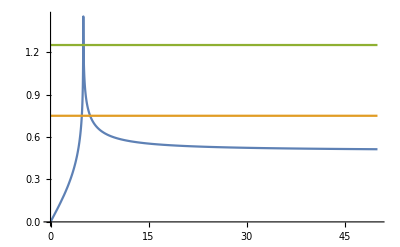

```mathematica
Plot[{Piecewise[{{{ψ[b]/(Pi 2)},0.001<b<ss},{{ϕ[b]/Pi},b>=ss}}],3/4,5/4},{b,0.001,50}]
```